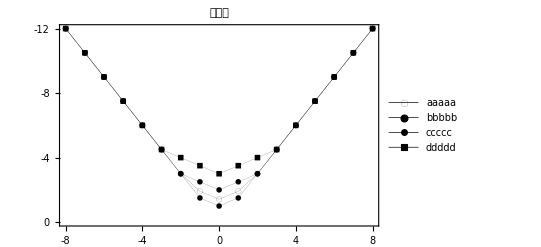

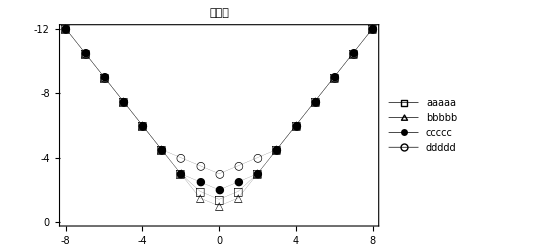

```mathematica
a={{-8,-12},{-7,-21/2},{-6,-9},{-5,-15/2},{-4,-6},{-3,-9/2},{-2,-3},{-1,(-2-4 √2)/4},{0,-√2},{1,(-2-4 √2)/4},{2,-3},{3,-9/2},{4,-6},{5,-15/2},{6,-9},{7,-21/2},{8,-12}};
b={{-8,-12},{-7,-21/2},{-6,-9},{-5,-15/2},{-4,-6},{-3,-9/2},{-2,-3},{-1,-3/2},{0,-1},{1,-3/2},{2,-3},{3,-9/2},{4,-6},{5,-15/2},{6,-9},{7,-21/2},{8,-12}};
c={{-8,-12},{-7,-21/2},{-6,-9},{-5,-15/2},{-4,-6},{-3,-9/2},{-2,-3},{-1,-5/2},{0,-2},{1,-5/2},{2,-3},{3,-9/2},{4,-6},{5,-15/2},{6,-9},{7,-21/2},{8,-12}};
d={{-8,-12},{-7,-21/2},{-6,-9},{-5,-15/2},{-4,-6},{-3,-9/2},{-2,-4},{-1,-7/2},{0,-3},{1,-7/2},{2,-4},{3,-9/2},{4,-6},{5,-15/2},{6,-9},{7,-21/2},{8,-12}};
{m1,m2,m3,m4}=Graphics/@{Circle[{0,0},1],Disk[{0,0},1],Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}],Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5}}]};

ListLinePlot[{a,b,c,d},Frame->True,AxesOrigin->{-8,0},FrameTicks->{{{0,-2,-4,-6,-8,-10,-12},None},{{-8,-6,-4,-2,0,2,4,6,8},None}},ScalingFunctions->{Identity,"Reverse"},PlotMarkers->Table[{s,0.02},{s,{m1,m2,m3,m4}}],PlotStyle->{{Black,Thickness[0.0002]},{Black,Thickness[0.0002]},{Black,Thickness[0.0002]},{Black,Thickness[0.0002]}},PlotLegends->PointLegend[{"aaaaa","bbbbb","ccccc","ddddd"},LegendMarkers->Automatic,LegendFunction->Frame],PlotLabel->"喵喵喵"]

ListLinePlot[{a,b,c,d},Frame->True,AxesOrigin->{-8,0},FrameTicks->{{{0,-2,-4,-6,-8,-10,-12},None},{{-8,-6,-4,-2,0,2,4,6,8},None}},ScalingFunctions->{Identity,"Reverse"},PlotMarkers->{"□","△","●","○"},PlotStyle->{{Black,Thickness[0.0002]},{Black,Thickness[0.0002]},{Black,Thickness[0.0002]},{Black,Thickness[0.0002]}},PlotLegends->Placed[PointLegend[{"aaaaa","bbbbb","ccccc","ddddd"},LegendMarkers->Automatic,LegendFunction->Frame],{0.5,0.75}],PlotLabel->"汪汪汪"]
```